# Cuaderno de Prácticas

#### ALGEBRA

### Grado en Ingeniería Informática

#### CURSO 2022/23.

## Datos Personales

Nombre y apellidos : Javier Francisco Dibo Gómez
DNI: 77646884B
Grupo de teoría: A
Grupo de prácticas: 2

## Sesion I

```mathematica
p[x_]:= x^7 +2x^3 -x^2 -5x
q[x_]:=x^2 +8
```

```mathematica
PolynomialMod[p[x],7]
PolynomialMod[q[x],7]
```

2 x+6 x^2+2 x^3+x^7

1+x^2

```mathematica
p[x_]:=2 x+6 x^2+2 x^3+x^7
q[x_]:=1+x^2
```

```mathematica
PowerMod[2,1,7]
```

2

```mathematica
p[x]*q[x]*2
```

2 (1+x^2) (2 x+6 x^2+2 x^3+x^7)

```mathematica
Euclides2[m_]:=Module[{p,q,d},If[Length[m]==3,p[x_]:=PolynomialMod[m[[1]],m[[3]]];
q[x_]:=PolynomialMod[m[[2]],m[[3]]];
d[x_]:=PolynomialQuotientRemainder[p[x],q[x],x,Modulus->m[[3]]];,p[x_]:=m[[1]];q[x_]:=m[[2]];
d[x_]:=PolynomialQuotientRemainder[p[x],q[x],x];];Print[p[x]," = (",q[x],") · (",d[x][[1]],") +",d[x][[2]]];If[Exponent[d[x][[2]],x]<0,Print["El máximo común divisor es"];
Return[q[x]],If[Length[m]==3,Euclides2[{q[x],d[x][[2]],m[[3]]}],Euclides2[{q[x],d[x][[2]]}]]]];
```

```mathematica
Clear[x];
Euclides2[{p[x],q[x]}]
```

2 x+6 x^2+2 x^3+x^7 = (1+x^2) · (6+3 x-x^3+x^5) +-6-x

1+x^2 = (-6-x) · (6-x) +37

-6-x = (37) · (-6/37-x/37) +0

El máximo común divisor es

37

```mathematica
PowerMod[37,1,7]
```

2

```mathematica
PolynomialGCD[p[x],q[x]]
```

1

En este caso salen distintas porque son asociados es decir, las unidades por las que multipliquemos hace que nos den polinomios distintos

Todos los MCD que hay son:
2 * 1 = 2 --> Este nos lo da la funcion Euclides2
2 * 2 = 4
2 * 3 = 6
2 * 4 = 1 --> Este nos lo da la funcion PolynomialGCD
2 * 5 = 3
2 * 6 = 5

```mathematica
IrreduciblePolynomialQ[6x^2+1, Extension->All]
```

False

False

False

Porque esta teniendo en cuenta los complejos, donde sí se puede reducir

```mathematica
Factor[6x^2+6]
```

6 (1+x^2)

```mathematica
Roots[6x^2+6==0,x]
```

x==ⅈ||x==-ⅈ

### Ejercicio 13.2

```mathematica
p[x_]:=x^5+3x^3+2x
q[x_]:=x^2+1
```

```mathematica
PolynomialGCD[p[x],q[x]]
```

1+x^2

```mathematica
PolynomialLCM[p[x],q[x]]
```

(1+x^2) (2 x+x^3)

```mathematica
Roots[p[x]==0,x]
```

x==0||x==ⅈ √2||x==-ⅈ √2||x==ⅈ||x==-ⅈ

```mathematica
Roots[q[x]==0,x]
```

x==ⅈ||x==-ⅈ

```mathematica
Factor[q[x]]
Factor[p[x]]
```

1+x^2

x (1+x^2) (2+x^2)

### Resolucion dada por ella

```mathematica
PolynomialGCD[x^7 +2x^3 -x^2 -5x,x^2 +8]
```

1

Todos los asociados de 2 en Ζ7 son:

```mathematica
Table[Mod[2*i,7],{i,1,6}]
```

{2,4,6,1,3,5}

```mathematica
PolynomialLCM[x^5+3x^3+2x,x^2+1]
```

(1+x^2) (2 x+x^3)

```mathematica
Expand[%]
```

2 x+3 x^3+x^5

Calcular mcd y mcm a traves de factorizacion, y las raices

```mathematica
q[x]
p[x]
```

1+x^2

2 x+3 x^3+x^5

```mathematica
Factor[1+x^2]
Factor[2 x+3 x^3+x^5]
```

1+x^2

x (1+x^2) (2+x^2)

```mathematica
Roots[x^2+1==0,x]
```

x==ⅈ||x==-ⅈ

NO tiene raices en Z

```mathematica
Roots[2 x+3 x^3+x^5==0,x]
```

x==0||x==ⅈ √2||x==-ⅈ √2||x==ⅈ||x==-ⅈ

La unica raiz en Z es x = 0 con multiplicidad 1

Resumen:
mcd  = 1 + x^2
mcm = 2x+3x^3+x^5

En C[x]

```mathematica
Factor[2 x+3 x^3+x^5, Extension->All]
```

x (-ⅈ+x) (ⅈ+x) (-ⅈ √2+x) (ⅈ √2+x)

Tiene las raices anteriores todas con mutiplicidad 1

```mathematica
Factor[x^2+1, Extension->All]
```

(-ⅈ+x) (ⅈ+x)

Tienes esas raices en C[x]

Las raices comunes son (-ⅈ+x) (ⅈ+x)

El mcm o el mcd es las raices comunes multiplicadas o algo no me acuerdo

## Sesion 2

### Funciones

```mathematica
(*Para las definiciones*)
G = {1};
operacion = {1};
```

Devuelve el elemento resultante de operar dos elementos:

```mathematica
op[x_,y_]:=operacion[[Position[G,x][[1]],Position[G,y][[1]]]][[1]][[1]];
```

Devuelve si la operacion es interna para un conjunto:

```mathematica
INTERNA[G_,operacion_]:=Module[{CONTADORi,interna},
(*Omitido para ahorrar espacio*)
```

Devuelve si existe o no neutro en un conjunto con operacion interna:

```mathematica
NEUTRO[G_,operacion_]:=Module[{CONTADORi},
(*Omitido para ahorrar espacio*)
```

Devuelve si el conjunto es simetrico para la operacion:

```mathematica
ELEMENTOSIMETRICO[G_,operacion_]:=Module[{CONTADORi,CONTADORj,Nosim,ElementoSimetrico,op,Neutro,salida},
(*Omitido para ahorrar espacio*)
```

Devuelve una tabla con los simetricos de cada elemento:

```mathematica
TABLAELEMENTOSIMETRICO[G_,operacion_]:=Module[{CONTADORi,CONTADORj,Nosim,ElementoSimetrico,op,Neutro,salida},
op[x_,y_]:=operacion[[Position[G,x][[1]],Position[G,y][[1]]]][[1]][[1]];
(*Omitido para ahorrar espacio*)
```

Devuelve el simetrico de un elemento dado:

```mathematica
SIMETRICO[x_,G_,operacion_]:=Module[{simetrico,CONTADORi,Neutro,op},
(*Omitido para ahorrar espacio*)
```

Devuelve si la operacion es asociativa para un grupo:

```mathematica
ASOCIATIVA[G_,operacion_]:=Module[{CONTADORi,CONTADORj,CONTADORk,asociativa,op},
(*Omitido para ahorrar espacio*)
```

Devuelve si una operacion es conmutativa para un grupo:

```mathematica
CONMUTATIVA[G_,operacion_]:=Module[{CONTADORi,CONTADORj,conmutativa,op},
(*Omitido para ahorrar espacio*)
```

Comprueba si un par (conjunto, operacion) es grupo:

```mathematica
GRUPO[Conjunto_,Operacion_]:=INTERNA[Conjunto,Operacion] && ELEMENTOSIMETRICO[Conjunto,Operacion]  && ASOCIATIVA[Conjunto,Operacion];
```

Comprueba si un par (conjunto, operacion) es grupo abeliano:

```mathematica
GRUPOABELIANO[Conjunto_,Operacion_]:=INTERNA[Conjunto,Operacion] && ELEMENTOSIMETRICO[Conjunto,Operacion] && ASOCIATIVA[Conjunto,Operacion] &&
   CONMUTATIVA[Conjunto,Operacion]
```

Comprueba si un grupo es subconjunto de otro

```mathematica
Clear[simetrico, CONTADORi];
SUBGRUPO[H_,G_,operacion_]:=Module[{subgrupo,CONTADORi,CONTADORj,op,simetrico,ElementoNeutro,neutro},
(*Omitido para ahorrar espacio*)
```

Dado un  grupo (G) se usa junto con el siguiente programa para CALCULAR TODOS LOS SUBGRUPOS

```mathematica
SUBGRUPOSN[n_]:=Module[{Subconjuntos,Subgrupos,CONTADORi},
(*Omitido para ahorrar espacio*)
```

Copy paste este programa para calcular todos los subgrupos

```mathematica
t=0;
cardinal=Divisors[Length[G]];
Do[
    subg=SUBGRUPOSN[cardinal[[CONTADORi]]];
    t=t+Length[subg];
    Print["Subgrupos de orden ",cardinal[[CONTADORi]],": ",subg]
    ,{CONTADORi,1,Length[cardinal]}];
Print["Número total de subgrupos: ",t]
```

Se comprobarán 2 subconjuntos de 1 elementos

Subgrupos de orden 1: {}

Número total de subgrupos: 0

### Ejercicio 1

#### A. Definir en G = ℤ6 una operación interna de manera que 3 sea el elemento neutro y que lo dote de estructura de grupo conmutativo. Hacer todas las comprobaciones explícitamente.

```mathematica
Clear[G,H,a,b,c,d,e,f]
G = {0,1,2,3,4,5};
```

```mathematica
operacion = {
  {3, 0, 1, 0, 2, 5},
  {0, 3, 4, 1, 3, 2},
  {1, 4, 3, 2, 1, 2},
  {0, 1, 2, 3, 4, 5},
  {2, 3, 1, 4, 3, 3},
  {5, 2, 2, 5, 3, 3}
};
INTERNA[G, operacion]
ELEMENTOSIMETRICO[G,operacion]
CONMUTATIVA[G,operacion]
```

True

Elemento neutro: 3

| 1 | 2 | 3 | 4 | 5 | 6
Elementos: | 0 | 1 | 2 | 3 | 4 | 5
Simétricos: | 0 | 1 | 2 | 3 | 1 | 4

True

True

Cumple las propiedades de operacion interna, simetrico, existencia de neutro, y conmutativa. Es grupo abeliano.

#### B. Demostrar si el subconjunto {1, 3} es un subgrupo de G.

```mathematica
Clear[H];
H = {1,3};
SUBGRUPO[H,G,operacion]
```

True

#### C. Demostrar si el subconjunto H = {2, 3, 5} es un subgrupo de G. En caso en que no lo sea, define una nueva operación de forma que G sea grupo con neutro 3 y H sea subgrupo suyo.

```mathematica
Clear[H];
H = {2,3,5};
SUBGRUPO[H,G,operacion]
```

False

```mathematica
opH = {
{5, 3, 2},
{3, 5, 5},
{2, 5, 3}
};
H = {2,5,3};
SUBGRUPO[H,G,operacion]
ELEMENTOSIMETRICO[H, opH]
```

False

Elemento neutro: 3

| 1 | 2 | 3
Elementos: | 2 | 5 | 3
Simétricos: | 5 | 2 | 3

True

### Ejercicio 2

-Graphics-

#### Apartado A

```mathematica
G = {a,b,c,9};
opG = {{9, c, b, a},
        {c, 9, a, b},
        {b, a, 9, c},
        {a, b, c, 9}};
 opG // MatrixForm
```

(9 | c | b | a
c | 9 | a | b
b | a | 9 | c
a | b | c | 9)

```mathematica
ELEMENTOSIMETRICO[G, opG]
```

Elemento neutro: 9

| 1 | 2 | 3 | 4
Elementos: | a | b | c | 9
Simétricos: | a | b | c | 9

True

```mathematica
CONMUTATIVA[G, opG]
```

True

#### Apartado B

(No funciona el código, se hizo a mano)

```mathematica
s1 = {9};
s2 = {a,9};
s3 = {b,9};
s4 = {c,9};
s5 = {a,b,c,9};
```

## Sesion 3

-Graphics-

#### Funciones

Funcion sigma

```mathematica
sigma[k_,n_][m_]:=Permutations[Table[j,{j,n}]][[k,m]]
```

Dado la n en la que estamos (Sn) me dice que permutacion completa es, formato S[n][[num]]

```mathematica
S[n_]:=Table[MatrixForm[{Table[j,{j,n}],Permutations[Table[j,{j,n}]][[i]]}],{i,n!}]
```

Calcular la composicion de dos permutaciones (Sk, Sj) en Sn

```mathematica
composicion[k_,j_,n_]:=Module[{t,m,z,tabla},
(*Omitido para ahorrar espacio*)
```

Calcular el numero de inversiones de una permutacion (escrita formato permutacion = {1, 2, ... n})

```mathematica
permutacion = {1, 2, n};
(*Omitido para ahorrar espacio*)
```

1

Calcular la permutacion inversa de una permutacion = {1,2,...,n}

```mathematica
(*Formato codigo no evaluable pq si no da error por el conjunto que se le pasa (perm)*)
InversePermutation[{1, 2, ..., n}]
```

Calcular la signatura de una permutacion = {1,2,...,n}, en Sn, con un indice de permutacion en ese Sn dado (k) - IMPORTANTE CARGAR LA FUNCION sigma DEL GUION “Sesion 03”

```mathematica
(*Formato codigo no evaluable pq si no da error por el conjunto que se le pasa (perm)*)
Clear[perm, n, k, ciclos, primero, imagen, cadena,signatura] 
perm="{1,2,...,n}";
n="NÚMERO DE ELEMENTOS DE LA PERMUTACIÓN";
k="ÍNDICE DE LA PERMUTACIÓN";
X=Table[i,{i,n}];
ciclos={};
While[X≠{},primero=X[[1]];
    imagen=primero;
    cadena={primero};
    While[sigma[k,n][imagen]≠primero,imagen=sigma[k,n][imagen];
      cadena=Append[cadena,imagen]];
    If[Length[cadena]>1,AppendTo[ciclos,cadena]];
    X=Complement[X,cadena];];
signatura=0;
Do[signatura=signatura+Length[ciclos[[i]]]-1,{i,1,Length[ciclos]}]
signatura=(-1)^signatura
```

Calcula el indice de una permutacion {1,2,...,n}

```mathematica
Indice[permutacion_]:=Position[Permutations[Table[j,{j,1,Length[permutacion]}]],permutacion][[1]][[1]]
```

Calcular la descomposicion en ciclos / transposiciones de cada permutacion

```mathematica
trasposiciones[ciclo_]:=Module[{cadena,i},
(*Omitido para ahorrar espacio*)
```

```mathematica
(*Formato codigo no evaluable pq si no da error por el conjunto que se le pasa*)
n = "NÚMERO DE ELEMENTOS DE LA PERMUTACIÓN"; 
k = "ÍNDICE DE LA PERMUTACIÓN"; 
X = Table[i, {i, n}]; 
ciclos = {}; 
While[X != {}, primero = X[[1]]; imagen = primero; 
    cadena = {primero}; While[sigma[k, n][imagen] != primero, 
     imagen = sigma[k, n][imagen]; cadena = 
       Append[cadena, imagen]]; If[Length[cadena] > 1, 
     AppendTo[ciclos, cadena]]; X = Complement[X, cadena]; ]; 
descomposicion = ""; 
Do[descomposicion = StringJoin[descomposicion, 
     trasposiciones[ciclos[[i]]]], {i, 1, Length[ciclos]}]; 
Print[σk, "=", S[n][[k]], "=", descomposicion]
```

#### Calculos de Sn

Determinar el numero de inversiones y la paridad de las siguientes permutaciones de S6:

```mathematica
dia = 7;
mes = 8;
anno = 2001;
dni = 77646884;
n = Mod[dni,304]+1;
m = dia * (Mod[mes*anno,13]+1);
```

```mathematica
composicion[n,m,6]
```

σ_117 σ_42=σ_75=(1 | 2 | 3 | 4 | 5 | 6
1 | 5 | 2 | 4 | 3 | 6)

```mathematica
S[6][[n]]
S[6][[m]]
```

(1 | 2 | 3 | 4 | 5 | 6
1 | 6 | 5 | 3 | 2 | 4)

(1 | 2 | 3 | 4 | 5 | 6
1 | 3 | 5 | 6 | 4 | 2)

```mathematica
PermutacionM = {1,6,5,3,2,4};
PermutacionN = {1,3,5,6,4,2};
PermutacionNM = {1,5,2,4,3,6};
PermutacionNMInversa = InversePermutation[PermutacionNM];
```

#### Calculo del indice de las permutaciones

```mathematica
Indice[PermutacionM]
```

117

#### Calculo del numero de inversiones

```mathematica
permutacion = PermutacionM;
inversion=0;
Do[
    Do[
        If[i<j && permutacion[[j]]< permutacion[[i]],inversion++];
        ,{j,i,Length[permutacion]}];
    ,{i,1,Length[permutacion]}];
inversion
```

8

El numero de inversiones de SigmaM es 8

```mathematica
permutacion = PermutacionN;
inversion=0;
Do[
    Do[
        If[i<j && permutacion[[j]]< permutacion[[i]],inversion++];
        ,{j,i,Length[permutacion]}];
    ,{i,1,Length[permutacion]}];
inversion
```

6

El numero de inversiones de SigmaN es 6

```mathematica
permutacion = PermutacionNM;
inversion=0;
Do[
    Do[
        If[i<j && permutacion[[j]]< permutacion[[i]],inversion++];
        ,{j,i,Length[permutacion]}];
    ,{i,1,Length[permutacion]}];
inversion
```

4

El numero de inversiones de SigmaNM es 4

```mathematica
permutacion = PermutacionNMInversa;
inversion=0;
Do[
    Do[
        If[i<j && permutacion[[j]]< permutacion[[i]],inversion++];
        ,{j,i,Length[permutacion]}];
    ,{i,1,Length[permutacion]}];
inversion
```

4

El numero de inversiones de SigmaNMInversa es 4

En resumen:

```mathematica
numInvN = 8;
numInvM = 6;
numInvNM = 4;
numInvNMInversa = 4;
```

#### Calcular la signatura

```mathematica
Clear[perm, n, k, ciclos, primero, imagen, cadena,signatura]
perm=PermutacionN;
n=6;
k=Indice[PermutacionN];
X=Table[i,{i,n}];
ciclos={};
While[X≠{},primero=X[[1]];
    imagen=primero;
    cadena={primero};
    While[sigma[k,n][imagen]≠primero,imagen=sigma[k,n][imagen];
      cadena=Append[cadena,imagen]];
    If[Length[cadena]>1,AppendTo[ciclos,cadena]];
    X=Complement[X,cadena];];
signatura=0;
Do[signatura=signatura+Length[ciclos[[i]]]-1,{i,1,Length[ciclos]}]
signatura=(-1)^signatura
```

1

```mathematica
Clear[perm, n, k, ciclos, primero, imagen, cadena,signatura]
perm=PermutacionM;
n=6;
k=Indice[PermutacionM];
X=Table[i,{i,n}];
ciclos={};
While[X≠{},primero=X[[1]];
    imagen=primero;
    cadena={primero};
    While[sigma[k,n][imagen]≠primero,imagen=sigma[k,n][imagen];
      cadena=Append[cadena,imagen]];
    If[Length[cadena]>1,AppendTo[ciclos,cadena]];
    X=Complement[X,cadena];];
signatura=0;
Do[signatura=signatura+Length[ciclos[[i]]]-1,{i,1,Length[ciclos]}]
signatura=(-1)^signatura
```

1

```mathematica
Clear[perm, n, k, ciclos, primero, imagen, cadena,signatura]
perm=PermutacionNM;
n=6;
k=Indice[PermutacionNM];
X=Table[i,{i,n}];
ciclos={};
While[X≠{},primero=X[[1]];
    imagen=primero;
    cadena={primero};
    While[sigma[k,n][imagen]≠primero,imagen=sigma[k,n][imagen];
      cadena=Append[cadena,imagen]];
    If[Length[cadena]>1,AppendTo[ciclos,cadena]];
    X=Complement[X,cadena];];
signatura=0;
Do[signatura=signatura+Length[ciclos[[i]]]-1,{i,1,Length[ciclos]}]
signatura=(-1)^signatura
```

1

```mathematica
Clear[perm, n, k, ciclos, primero, imagen, cadena,signatura]
perm=PermutacionNMInversa;
n=6;
k=Indice[PermutacionNMInversa];
X=Table[i,{i,n}];
ciclos={};
While[X≠{},primero=X[[1]];
    imagen=primero;
    cadena={primero};
    While[sigma[k,n][imagen]≠primero,imagen=sigma[k,n][imagen];
      cadena=Append[cadena,imagen]];
    If[Length[cadena]>1,AppendTo[ciclos,cadena]];
    X=Complement[X,cadena];];
signatura=0;
Do[signatura=signatura+Length[ciclos[[i]]]-1,{i,1,Length[ciclos]}]
signatura=(-1)^signatura
```

1

Todas las signaturas son positivas (pues sus numero de inversiones eras pares)

#### Ejercicio 2 (13 rel 2)

Dadas las permutaciones de S5 
σ = {{ 1, 2, 3, 4, 5},{ 2, 3, 1, 5, 4}}
τ = {{ 1, 2, 3, 4, 5},{ 5, 4, 1, 3, 2} 
Se pide: 
i) El numero de inversiones de cada permutacion. 
ii) La descomposicion en ciclos y transposiciones de cada permutacion. 
iii) La signatura de cada permutacion.

i) El numero de inversiones de cada permutacion.:

```mathematica
pSigma = { 2, 3, 1, 5, 4};
pTau =  { 5, 4, 1, 3, 2};
```

Numero de inversiones:

```mathematica
permutacion = pSigma;
inversion=0;
Do[
    Do[
        If[i<j && permutacion[[j]]< permutacion[[i]],inversion++];
        ,{j,i,Length[permutacion]}];
    ,{i,1,Length[permutacion]}];
inversion
```

3

```mathematica
permutacion = pTau;
inversion=0;
Do[
    Do[
        If[i<j && permutacion[[j]]< permutacion[[i]],inversion++];
        ,{j,i,Length[permutacion]}];
    ,{i,1,Length[permutacion]}];
inversion
```

8

ii) La descomposicion en ciclos y transposiciones de cada permutacion :
Necesitamos saber el indice de la permutacion:

```mathematica
Indice[pSigma]
Indice[pTau]
```

32

116

Los indices son, pSigma=32, pTau=116

```mathematica
n = 5; 
k = 32; 
X = Table[i, {i, n}]; 
ciclos = {}; 
While[X != {}, primero = X[[1]]; imagen = primero; 
    cadena = {primero}; While[sigma[k, n][imagen] != primero, 
     imagen = sigma[k, n][imagen]; cadena = 
       Append[cadena, imagen]]; If[Length[cadena] > 1, 
     AppendTo[ciclos, cadena]]; X = Complement[X, cadena]; ]; 
descomposicion = ""; 
Do[descomposicion = StringJoin[descomposicion, 
     trasposiciones[ciclos[[i]]]], {i, 1, Length[ciclos]}]; 
Print[σk, "=", S[n][[k]], "=", descomposicion]
```

σk=(1 | 2 | 3 | 4 | 5
2 | 3 | 1 | 5 | 4)=(1 3)(1 2)(4 5)

```mathematica
n = 5; 
k = 116; 
X = Table[i, {i, n}]; 
ciclos = {}; 
While[X != {}, primero = X[[1]]; imagen = primero; 
    cadena = {primero}; While[sigma[k, n][imagen] != primero, 
     imagen = sigma[k, n][imagen]; cadena = 
       Append[cadena, imagen]]; If[Length[cadena] > 1, 
     AppendTo[ciclos, cadena]]; X = Complement[X, cadena]; ]; 
descomposicion = ""; 
Do[descomposicion = StringJoin[descomposicion, 
     trasposiciones[ciclos[[i]]]], {i, 1, Length[ciclos]}]; 
Print[σk, "=", S[n][[k]], "=", descomposicion]
```

σk=(1 | 2 | 3 | 4 | 5
5 | 4 | 1 | 3 | 2)=(1 3)(1 4)(1 2)(1 5)

iii) La signatura de cada permutacion .

```mathematica
Clear[perm, n, k, ciclos, primero, imagen, cadena,signatura]
perm=pSigma;
n=6;
k=Indice[PermutacionNMInversa];
X=Table[i,{i,n}];
ciclos={};
While[X≠{},primero=X[[1]];
    imagen=primero;
    cadena={primero};
    While[sigma[k,n][imagen]≠primero,imagen=sigma[k,n][imagen];
      cadena=Append[cadena,imagen]];
    If[Length[cadena]>1,AppendTo[ciclos,cadena]];
    X=Complement[X,cadena];];
signatura=0;
Do[signatura=signatura+Length[ciclos[[i]]]-1,{i,1,Length[ciclos]}]
signatura=(-1)^signatura
```

1

La signatura de pSigma es 1

```mathematica
Clear[perm, n, k, ciclos, primero, imagen, cadena,signatura]
perm=pTau;
n=6;
k=Indice[PermutacionNMInversa];
X=Table[i,{i,n}];
ciclos={};
While[X≠{},primero=X[[1]];
    imagen=primero;
    cadena={primero};
    While[sigma[k,n][imagen]≠primero,imagen=sigma[k,n][imagen];
      cadena=Append[cadena,imagen]];
    If[Length[cadena]>1,AppendTo[ciclos,cadena]];
    X=Complement[X,cadena];];
signatura=0;
Do[signatura=signatura+Length[ciclos[[i]]]-1,{i,1,Length[ciclos]}]
signatura=(-1)^signatura
```

1

La signatura de pTau es 1

## Sesion 4

-Graphics-

#### Funciones

Calculo de la matriz de ayacencia de un grafo NO ORIENTADO

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
(*Omitido para ahorrar espacio*)
```

Calculo de la matriz de ayacencia de un grafo ORIENTADO / DIRIGIDO

```mathematica
MATRIZADYACENCIADIR[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
(*Omitido para ahorrar espacio*)
```

Dada una matriz de ayacencia, calcula los vertices y lados de un grafo NO ORIENTADO

```mathematica
(*Celda no evaluable*)
Clear[matrizadyacencia, W, F]
matrizadyacencia="MATRIZ DE ADYACENCIA";
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F
```

Dada una matriz de ayacencia, calcula los vertices y lados de un grafo ORIENTADO / DIRIGIDO

```mathematica
(*Celda no evaluable*)
Clear[matrizadyacencia, W, F]
matrizadyacencia="MATRIZ DE ADYACENCIA";
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];
        ,{i,Dimensions[matrizadyacencia][[1]]}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F
```

Calculo de la matriz de Incidencia

```mathematica
MATRIZINCIDENCIA[W_,F_]:=Module[{i,j,nuevoF,CONTADORi},
(*Omitido para ahorrar espacio*)
```

Dada una matriz de ayacendcia, da su representacion grafica

```mathematica
GraphPlot["MATRIZ DE ADAYACENCIA"];
```

Calcula si dos matrices dadas son isomorfas

```mathematica
ISOMORFOS[A1_,A2_]:=Module[{matricesP,i,j},
(*Omitido para ahorrar espacio*)
```

#### Grafos

```mathematica
(*Grafos ejercicio 5.4*)
Clear[F1,A2,F3,A4,A5,F6]
F1 = {1->2,1->4,2->1,2->3,3->2,3->6,6->3,6->5,5->6,5->4,4->5,4->1};
A2 = {{0,1,0,0,0,1},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,0,0,0,1,0}};
F3 = {1->6,1->5,2->4,2->6,3->4,3->5,4->2,4->3,5->1,5->3,6->1,6->2};
A4 = {{0,1,0,0,0,1},{1,0,0,0,0,1},{0,0,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,1,0,0,1,0}};
A5 = {{1,0,0,1,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,1,0,0,0,1},{0,1,0,0,1,0},{1,0,0,0,0,1}};
F6 = {1->2,1->3,2->3,3->5,4->5,4->6,5->6};
```

#### Ejercicio 1

-Graphics-

```mathematica
Clear[W]
W = {1,2,3,4,5,6};
```

Calcular los vertices y lados de las matrices

```mathematica
Clear[matrizadyacencia, W, F]
matrizadyacencia=A2;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F;
F2 = F
```

{1→2,2→3,3→4,4→5,1→6,5→6}

```mathematica
Clear[matrizadyacencia, W, F]
matrizadyacencia=A4;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F;
F4 = F
```

{1→2,3→4,4→5,1→6,2→6,5→6}

```mathematica
Clear[matrizadyacencia, W, F]
matrizadyacencia=A5;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F;
F5 = F
```

{1→1,2→2,3→3,1→4,2→4,3→5,5→5,6→6}

Calcular las matrices de los vertices y lados

```mathematica
Clear[A1,A3,A6]
A1 = MATRIZADYACENCIA[W,F1];
A3 = MATRIZADYACENCIA[W,F3];
A6 = MATRIZADYACENCIA[W,F6];
```

Calcular las matrices de incidencia

```mathematica
Clear[I1,I2,I3,I4,I5,I6]
I1 = MATRIZINCIDENCIA[W,F1];
I2 = MATRIZINCIDENCIA[W,F2];
I3 = MATRIZINCIDENCIA[W,F3];
I4 = MATRIZINCIDENCIA[W,F4];
I5 = MATRIZINCIDENCIA[W,F5];
I6 = MATRIZINCIDENCIA[W,F6];
```

Representacion grafica

```mathematica
GraphPlot[A1];
```

#### Ejercicio 2

-Graphics-

```mathematica
Clear[F1,F2,F3,A4,F5]
F1 = {1->5,2->6,3->4,4->2,5->2,5->3,6->1};
F2 = {1->3,2->5,3->6,4->2,5->1,6->5,6->4};
F3 = {1->2,2->3,2->5,3->4,4->5,5->6,6->1};
A4 = {{0,1,0,0,0,1},{0,0,1,0,1,0},{1,0,0,0,0,0},{0,0,1,0,1,0},{0,0,0,0,0,0},{0,0,0,1,1,0}};
F5 = {1->4,2->3,6->1,3->5,4->6,5->6};
```

Calcular matriz de ayacencia

```mathematica
Clear[A1,A2,A3,A5,W]
W = {1,2,3,4,5,6};
A1 = MATRIZADYACENCIADIR[W,F1];
A2 = MATRIZADYACENCIADIR[W,F2];
A3 = MATRIZADYACENCIADIR[W,F3];
A5 = MATRIZADYACENCIADIR[W,F5];
```

Calcular vertices y lados

```mathematica
Clear[matrizadyacencia, W, F]
matrizadyacencia=A4;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];
        ,{i,Dimensions[matrizadyacencia][[1]]}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F4 = F;
```

Representacion grafica

```mathematica
GraphPlot[A1];
GraphPlot[A2];
GraphPlot[A3];
GraphPlot[A4];
GraphPlot[A5];
```

#### Ejercicio 3

-Graphics-

-Graphics-

Grafos dados

```mathematica
Clear[F1,A2,F3,A4,A5,F6,W]
W = {1,2,3,4,5,6};
F1 = {1->2,1->4,2->1,2->3,3->2,3->6,6->3,6->5,5->6,5->4,4->5,4->1};
A2 = {{0,1,0,0,0,1},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,0,0,0,1,0}};
F3 = {1->6,1->5,2->4,2->6,3->4,3->5,4->2,4->3,5->1,5->3,6->1,6->2};
A4 = {{0,1,0,0,0,1},{1,0,0,0,0,1},{0,0,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,1,0,0,1,0}};
A5 = {{1,0,0,1,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,1,0,0,0,1},{0,1,0,0,1,0},{1,0,0,0,0,1}};
F6 = {1->2,1->3,2->3,3->5,4->5,4->6,5->6};
```

Matriz de los grafos que fueros dados en formato grafico

```mathematica
Clear[A1,A3,A6]
A1 = MATRIZADYACENCIA[W,F1];
A3 = MATRIZADYACENCIA[W,F3];
A6 = MATRIZADYACENCIA[W,F6];
```

Calculo de isomorfismos

```mathematica
ISOMORFOS[A1,A2]
```

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 3 | 6 | 5 | 4)

```mathematica
ISOMORFOS[A1,A3]
```

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 3 | 5 | 6 | 4 | 2)

```mathematica
ISOMORFOS[A1,A4]
```

No son isomorfos

```mathematica
ISOMORFOS[A1,A5]
```

No son isomorfos

```mathematica
ISOMORFOS[A1,A6]
```

No son isomorfos

```mathematica
ISOMORFOS[A4,A5]
```

No son isomorfos

```mathematica
ISOMORFOS[A4,A6]
```

No son isomorfos

```mathematica
ISOMORFOS[A5,A6]
```

No son isomorfos

A1, A2 y A3 son isomorfos. El resto son unicos.

## Sesion 5

#### Funciones

Dado un conjunto de vertices y un conjunto de lados, da la matriz de ayacencia

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
(*Omitido para ahorrar espacio*)
```

Dada una matriz de ayacencia, calcula si es regular o no

```mathematica
(*Omitido para ahorrar espacio*)
```

Dada una matriz de ayacencia calcula si es completo o no

```mathematica
COMPLETO[matrizadyacencia_]:=  (Sum[MatrixPower[matrizadyacencia,2][[i,i]],{i,Dimensions[matrizadyacencia][[1]]}]==Dimensions[matrizadyacencia][[1]]*(Dimensions[matrizadyacencia][[1]]-1))
```

Dado un conjunto de vertices y un conjunto de lados, dice si es bipartito o no (hay que cargar el paquete)

```mathematica
IND[W1_,F_]:=Module[{i},
(*Omitido para ahorrar espacio*)
```

```mathematica
BIPARTITO[W_,F_]:=Module[{i,subconjuntos,j,fin},
(*Omitido para ahorrar espacio*)
```

#### Grafos

Matrices

```mathematica
A2 = {{0,1,0,0,0,1},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,0,0,0,1,0}};
A4 = {{0,1,0,0,0,1},{1,0,0,0,0,1},{0,0,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,1,0,0,1,0}};
A5 = {{1,0,0,1,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,1,0,0,1},{0,1,0,0,1,0},{1,0,0,0,0,1}};
```

Lados

```mathematica
F1 = {1->2,1->4,2->1,2->3,3->2,3->6,6->3,6->5,5->6,5->4,4->5,4->1};
F3 = {1->6,1->5,2->4,2->6,3->4,3->5,4->2,4->3,5->1,5->3,6->1,6->2};
F6 = {1->2,1->3,2->3,3->5,4->5,4->6,5->6};
K6 = {1->2,1->3,1->4,1->5,1->6,2->1,2->3,2->4,2->5,2->6,3->1,3->2,3->4,3->5,3->6,4->1,4->2,4->3,4->5,4->6,5->1,5->2,5->3,5->4,5->6,6->1,6->2,6->3,6->4,6->5};
K33 = {1->4,1->5,1->6,2->4,2->5,2->6,3->4,3->5,3->6,4->1,4->2,4->3,5->1,5->2,5->3,6->1,6->2,6->3};
Octogono = {1->2,1->8,2->1,2->3,3->2,3->4,4->3,4->5,5->4,5->6,6->5,6->7,7->6,7->8,8->1};
```

```mathematica
W6 = {1,2,3,4,5,6};
A1 = MATRIZADYACENCIA[W6,F1];
A3 = MATRIZADYACENCIA[W6,F3];
A6 = MATRIZADYACENCIA[W6,F6];
AK6 = MATRIZADYACENCIA[W6,K6];
AK33 = MATRIZADYACENCIA[W6,K33];
W8 = {1,2,3,4,5,6,7,8};
AOct= MATRIZADYACENCIA[W8,Octogono];
```

```mathematica
Clear[matrizadyacencia, W, F]
matrizadyacencia=A2;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F2 = F
```

{1→2,2→3,3→4,4→5,1→6,5→6}

```mathematica
Clear[matrizadyacencia, W, F]
matrizadyacencia=A4;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F4 = F
```

{1→2,3→4,4→5,1→6,2→6,5→6}

```mathematica
Clear[matrizadyacencia, W, F]
matrizadyacencia=A5;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F5 = F
```

{1→1,2→2,3→3,1→4,2→4,3→5,5→5,4→6,6→6}

#### Ejercicio 1

-Graphics-

```mathematica
{"A1:",REGULAR[A1],COMPLETO[A1]}
BIPARTITO[W6,F1]
```

{A1:,True,False}

Es bipartito: W1={1,3,5} y W2={2,4,6}

No es bipartito completo

```mathematica
{"A2:",REGULAR[A2],COMPLETO[A2]}
BIPARTITO[W6,F2]
```

{A2:,True,False}

Es bipartito: W1={1,3,5} y W2={2,4,6}

No es bipartito completo

```mathematica
{"A3:",REGULAR[A3],COMPLETO[A3]}
BIPARTITO[W6,F3]
```

{A3:,True,False}

Es bipartito: W1={1,2,3} y W2={4,5,6}

No es bipartito completo

```mathematica
{"A4:",REGULAR[A4],COMPLETO[A4]}
BIPARTITO[W6,F4]
```

{A4:,False,False}

No es bipartito

```mathematica
{"A5:",REGULAR[A5],COMPLETO[A5]}
BIPARTITO[W6,F5]
```

{A5:,True,False}

Es bipartito: W1={3,4} y W2={1,2,5,6}

No es bipartito completo

```mathematica
{"A6:",REGULAR[A6],COMPLETO[A6]}
BIPARTITO[W6,F6]
```

{A6:,False,False}

No es bipartito

```mathematica
{"AK33:",REGULAR[AK33],COMPLETO[AK33]}
BIPARTITO[W6,K33]
```

{AK33:,True,False}

Es bipartito: W1={1,2,3} y W2={4,5,6}

No es bipartito completo

```mathematica
{"AK6:",REGULAR[AK6],COMPLETO[AK6]}
BIPARTITO[W6,K6]
```

{AK6:,True,True}

No es bipartito

```mathematica
{"AOct:",REGULAR[AOct],COMPLETO[AOct]}
BIPARTITO[W8,Octogono]
```

{AOct:,True,False}

Es bipartito: W1={1,3,5,7} y W2={2,4,6,8}

No es bipartito completo

#### Ejercicio 2

-Graphics-

```mathematica
W8 = {1,2,3,4,5,6,7,8};
F1617 = {1->3,1->7,2->8,2->4,3->1,3->5,4->2,4->6,5->3,5->7,6->4,6->8,7->1,7->5,8->6,8->2};
A1617 = MATRIZADYACENCIA[W8,F1617];
```

```mathematica
{"A1617:",REGULAR[A1617],COMPLETO[A1617]}
BIPARTITO[W8,F1617]
```

{A1617:,True,False}

Es bipartito: W1={1,2,5,6} y W2={3,4,7,8}

Es bipartito completo: K_(4,4)

Como se puede observar, es bipartito completo.

## Sesion 6

#### Funciones

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
(*Omitido para ahorrar espacio*)
```

Esta funcion devuelve el camino. NO TIENE *NADA* QUE VER CON EL TEOREMA DEL NUMERO DE CAMINOS. NO APLICAR PARA ESO. Simplemente te dice el camino
Dados dos vertices, una distancia y una matriz, te devuelve el camino

```mathematica
CAMINOS[vertice1_,vertice2_,longitud_,matrizadyacencia_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
(*Omitido para ahorrar espacio*)
```

Dada una matriz de adyacencia, devuelve si es conexo o no

```mathematica
CONEXO[A_]:=Module[{i,j,B},
(*Omitido para ahorrar espacio*)
```

Dada una matriz de adyacencia devuelve sus componentes conexas

```mathematica
COMPONENTESCONEXAS[matrizadyacencia_]:=Module[{j,B,conjunto,temp},
(*Omitido para ahorrar espacio*)
```

Dada la matriz de adyacencia, devuelve si es o no grafo de Euler

```mathematica
EULER[matrizadyacencia_]:=Module[{A,i},
(*Omitido para ahorrar espacio*)
```

Dada una matriz de ayacencia devuelve el camino de Hamilton

```mathematica
HAMILTON[A_]:=Module[{ciclos,adyacentes,ultvertice,ciclostemp,k,t,j,i},
(*Omitido para ahorrar espacio*)
```

Para saber si es de Hamilton (true o false) usar: HamiltonianGraphQ[]

Dados dos vertices y una matriz de adyacencia, su distancia

```mathematica
distancia[u_,v_,matrizadyacencia_]:=Module[{B},
(*Omitido para ahorrar espacio*)
```

Dados dos vertices y una matriz de adyacencia, sus geodesicas

```mathematica
GEODESICAS[u_,v_,matrizadyacencia_]:=Module[{B},
(*Omitido para ahorrar espacio*)
```

Devuelve el ciclo de Euler dada una matriz de ayacencia (L)

```mathematica
matrizadyacencia=G;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
,{j,Dimensions[matrizadyacencia][[1]]}];
tempF=F;
listaciclos={};
While[tempF≠{},
    camino={};
    inicio=tempF[[1,1]];
    otro=tempF[[1,2]];
    AppendTo[camino,tempF[[1,1]]];
    AppendTo[camino,tempF[[1,2]]];
    tempF=Complement[tempF,{tempF[[1]]}];
    While[otro≠inicio,
      j=1;
      ultimo=Last[camino];
      While[tempF[[j,1]]≠ultimo && tempF[[j,2]]≠ultimo ,j++];
      otro=Complement[{tempF[[j]][[1]],tempF[[j]][[2]]},{ultimo}][[1]];
      AppendTo[camino,otro];
      tempF=Complement[tempF,{tempF[[j]]}];
      ];
    AppendTo[listaciclos,camino];
    ];
nuevociclo=listaciclos[[1]];
While[Length[listaciclos]≠1,
    i=2;
    While[Intersection[listaciclos[[1]],listaciclos[[i]]]=={},i++];
    opcion=Intersection[listaciclos[[1]],listaciclos[[i]]][[1]];
    k1=Position[listaciclos[[1]],opcion][[1]][[1]];
    k2=Position[listaciclos[[i]],opcion][[1]][[1]];
    nuevociclo=listaciclos[[1]];
    t=1;
    Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,k2+1,Length[listaciclos[[i]]]}];
    Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,2,k2}];
    listaciclos=Delete[listaciclos,i];
    listaciclos=Delete[listaciclos,1];
    AppendTo[listaciclos,nuevociclo];
    ];
nuevociclo
```

#### Ejercicio 1

-Graphics-

#### Grafos

```mathematica
A2 = {{0,1,0,0,0,1},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,0,0,0,1,0}};
A4 = {{0,1,0,0,0,1},{1,0,0,0,0,1},{0,0,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,1,0,0,1,0}};
A5 = {{1,0,0,1,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,1,0,0,1},{0,1,0,0,1,0},{1,0,0,0,0,1}};
```

```mathematica
F1 = {1->2,1->4,2->1,2->3,3->2,3->6,6->3,6->5,5->6,5->4,4->5,4->1};
F3 = {1->6,1->5,2->4,2->6,3->4,3->5,4->2,4->3,5->1,5->3,6->1,6->2};
F6 = {1->2,1->3,2->3,3->5,4->5,4->6,5->6};
K6 = {1->2,1->3,1->4,1->5,1->6,2->1,2->3,2->4,2->5,2->6,3->1,3->2,3->4,3->5,3->6,4->1,4->2,4->3,4->5,4->6,5->1,5->2,5->3,5->4,5->6,6->1,6->2,6->3,6->4,6->5};
K33 = {1->4,1->5,1->6,2->4,2->5,2->6,3->4,3->5,3->6,4->1,4->2,4->3,5->1,5->2,5->3,6->1,6->2,6->3};
Octogono = {1->2,1->8,2->1,2->3,3->2,3->4,4->3,4->5,5->4,5->6,6->5,6->7,7->6,7->8,8->1};
F1617 = {1->3,1->7,2->8,2->4,3->1,3->5,4->2,4->6,5->3,5->7,6->4,6->8,7->1,7->5,8->6,8->2};
```

```mathematica
W6 = {1,2,3,4,5,6};
A1 = MATRIZADYACENCIA[W6,F1];
A3 = MATRIZADYACENCIA[W6,F3];
A6 = MATRIZADYACENCIA[W6,F6];
AK6 = MATRIZADYACENCIA[W6,K6];
AK33 = MATRIZADYACENCIA[W6,K33];
W8 = {1,2,3,4,5,6,7,8};
AOct= MATRIZADYACENCIA[W8,Octogono];
A1617 = MATRIZADYACENCIA[W8, F1617];
```

Nota : lo divido en dos por comodidad

#### Apartado i

-Graphics-

```mathematica
{CONEXO[A1], CONEXO[A2],CONEXO[A3],CONEXO[A4],CONEXO[A5],CONEXO[A6]}
```

{True,True,True,True,True,True}

```mathematica
{CONEXO[AK6],CONEXO[AK33],CONEXO[AOct],CONEXO[A1617]}
```

{True,True,True,False}

#### Apartado ii

-Graphics-

```mathematica
{COMPONENTESCONEXAS[A1], COMPONENTESCONEXAS[A2],COMPONENTESCONEXAS[A3],COMPONENTESCONEXAS[A4],COMPONENTESCONEXAS[A5],COMPONENTESCONEXAS[A6]}
```

{{{1,2,3,4,5,6}},{{1,2,3,4,5,6}},{{1,2,3,4,5,6}},{{1,2,3,4,5,6}},{{1,2,3,4,5,6}},{{1,2,3,4,5,6}}}

```mathematica
{COMPONENTESCONEXAS[AK6],COMPONENTESCONEXAS[AK33],COMPONENTESCONEXAS[AOct],COMPONENTESCONEXAS[A1617]}
```

{{{1,2,3,4,5,6}},{{1,2,3,4,5,6}},{{1,2,3,4,5,6,7,8}},{{1,3,5,7},{2,4,6,8}}}

#### Apartado iii

-Graphics-

```mathematica
{EULER[A1], EULER[A2],EULER[A3],EULER[A4],EULER[A5],EULER[A6]}
```

{True,True,True,False,False,False}

```mathematica
{EULER[AK6],EULER[AK33],EULER[AOct],EULER[A1617]}
```

{False,False,True,False}

#### Apartado iv

-Graphics-

```mathematica
{HamiltonianGraphQ[A1], HamiltonianGraphQ[A2],HamiltonianGraphQ[A3],HamiltonianGraphQ[A4],HamiltonianGraphQ[A5],HamiltonianGraphQ[A6]}
```

{False,False,False,False,False,False}

```mathematica
{HamiltonianGraphQ[AK6],HamiltonianGraphQ[AK33],HamiltonianGraphQ[AOct],HamiltonianGraphQ[A1617]}
```

{False,False,False,False}

#### Apartado v y vi

-Graphics-

-Graphics-

Primero:

```mathematica
distancia[1,6,A1](*Num de vertices*)
```

2 geodésica/s. Distancia: 3

```mathematica
CAMINOS[1,6,3,A1](*Distancia 3*)
```

{{1,2,3,6},{1,4,5,6}}

```mathematica
EULER[A1]
```

True

```mathematica
matrizadyacencia=A1;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
,{j,Dimensions[matrizadyacencia][[1]]}];
tempF=F;
listaciclos={};
While[tempF≠{},
    camino={};
    inicio=tempF[[1,1]];
    otro=tempF[[1,2]];
    AppendTo[camino,tempF[[1,1]]];
    AppendTo[camino,tempF[[1,2]]];
    tempF=Complement[tempF,{tempF[[1]]}];
    While[otro≠inicio,
      j=1;
      ultimo=Last[camino];
      While[tempF[[j,1]]≠ultimo && tempF[[j,2]]≠ultimo ,j++];
      otro=Complement[{tempF[[j]][[1]],tempF[[j]][[2]]},{ultimo}][[1]];
      AppendTo[camino,otro];
      tempF=Complement[tempF,{tempF[[j]]}];
      ];
    AppendTo[listaciclos,camino];
    ];
nuevociclo=listaciclos[[1]];
While[Length[listaciclos]≠1,
    i=2;
    While[Intersection[listaciclos[[1]],listaciclos[[i]]]=={},i++];
    opcion=Intersection[listaciclos[[1]],listaciclos[[i]]][[1]];
    k1=Position[listaciclos[[1]],opcion][[1]][[1]];
    k2=Position[listaciclos[[i]],opcion][[1]][[1]];
    nuevociclo=listaciclos[[1]];
    t=1;
    Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,k2+1,Length[listaciclos[[i]]]}];
    Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,2,k2}];
    listaciclos=Delete[listaciclos,i];
    listaciclos=Delete[listaciclos,1];
    AppendTo[listaciclos,nuevociclo];
    ];
nuevociclo
```

{1,2,3,6,5,4,1}

```mathematica
GEODESICAS[1,6,A1] (* Camino del 1 al 6*)
```

{{1,2,3,6},{1,4,5,6}}

Segundo:

```mathematica
distancia[1,6,A2] (*Num de vertices*)
```

1 geodésica/s. Distancia: 1

```mathematica
CAMINOS[1,6,1,A2] (*Distancia 1*)
```

{{1,6}}

```mathematica
GEODESICAS[1,6,A2] (* Camino del 1 al 6*)
```

{{1,6}}

```mathematica
EULER[A2]
```

True

```mathematica
matrizadyacencia=A2;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
,{j,Dimensions[matrizadyacencia][[1]]}];
tempF=F;
listaciclos={};
While[tempF≠{},
    camino={};
    inicio=tempF[[1,1]];
    otro=tempF[[1,2]];
    AppendTo[camino,tempF[[1,1]]];
    AppendTo[camino,tempF[[1,2]]];
    tempF=Complement[tempF,{tempF[[1]]}];
    While[otro≠inicio,
      j=1;
      ultimo=Last[camino];
      While[tempF[[j,1]]≠ultimo && tempF[[j,2]]≠ultimo ,j++];
      otro=Complement[{tempF[[j]][[1]],tempF[[j]][[2]]},{ultimo}][[1]];
      AppendTo[camino,otro];
      tempF=Complement[tempF,{tempF[[j]]}];
      ];
    AppendTo[listaciclos,camino];
    ];
nuevociclo=listaciclos[[1]];
While[Length[listaciclos]≠1,
    i=2;
    While[Intersection[listaciclos[[1]],listaciclos[[i]]]=={},i++];
    opcion=Intersection[listaciclos[[1]],listaciclos[[i]]][[1]];
    k1=Position[listaciclos[[1]],opcion][[1]][[1]];
    k2=Position[listaciclos[[i]],opcion][[1]][[1]];
    nuevociclo=listaciclos[[1]];
    t=1;
    Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,k2+1,Length[listaciclos[[i]]]}];
    Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,2,k2}];
    listaciclos=Delete[listaciclos,i];
    listaciclos=Delete[listaciclos,1];
    AppendTo[listaciclos,nuevociclo];
    ];
nuevociclo
```

{1,2,3,4,5,6,1}

Tercero:

```mathematica
...
```

Cuarto grafo:

Quinto grafo:

etc...

## Sesion 7

#### Funciones

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
(*Omitido para ahorrar espacio*)
```

Dada una matriz de adyacencia, devuelve el numero cromatico

```mathematica
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
(*Omitido para ahorrar espacio*)
```

Dada una matriz de adyacencia, devuelve si es plano

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
(*Omitido para ahorrar espacio*)
```

```mathematica
ARBOL[matrizadyacencia_]:=Module[{i,j,lados},
(*Omitido para ahorrar espacio*)
```

Dada una matriz de adyacencia, devuelve una coloracion optima

```mathematica
DIBUJAR[matrizadyacencia_]:=Module[{colores,colorear,COLORES,i},NUMEROCROMATICO[matrizadyacencia];colorear=coloraciones⟦1⟧;colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]
]
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
(*Omitido para ahorrar espacio*)
```

#### Ejercicio 1

-Graphics-

#### a.i.

```mathematica
W={1,2,3,4,5,6};
F={1->2,2->3,3->6,6->5,5->4,4->1};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

-Graphics-

#### a.ii.

```mathematica
W={1,2,3,4,5,6};
F={1->2,2->3,3->4,4->5,5->6,6->1};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

-Graphics-

#### a.iii.

```mathematica
W={1,2,3,4,5,6};
F={1->6,2->4,3->5,4->3,5->1,6->2};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

Vértice 6, color Rojo

-Graphics-

#### a.iv.

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

Vértice 6, color Rojo

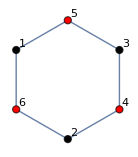

```mathematica
W={1,2,3,4,5,6};
F={1->6,2->4,3->5,4->3,5->1,6->2};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### a.v.

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Negro

Vértice 5, color Negro

Vértice 6, color Rojo

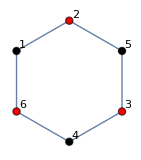

```mathematica
W={1,2,3,4,5,6};
F={1->6,2->5,3->4,1->2,3->5,4->6};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### a.vi.

{Numero cromatico:,3}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Negro

Vértice 5, color Rojo

Vértice 6, color Verde

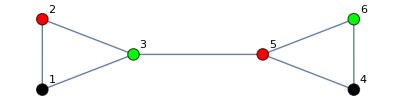

```mathematica
W={1,2,3,4,5,6};
F={1->2,1->3,2->3,3->5,4->5,4->6,5->6};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### octogono.

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Rojo

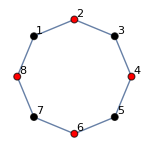

```mathematica
W={1,2,3,4,5,6,7,8};
F={1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->1};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### k6.

{Numero cromatico:,6}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Azul

Vértice 5, color Amarillo

Vértice 6, color Cyan

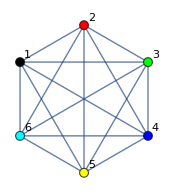

```mathematica
W={1,2,3,4,5,6};
F={2->1,3->1,4->1,5->1,6->1,1->2,3->2,4->2,5->2,6->2,1->3,2->3,4->3,5->3,6->3,1->4,2->4,3->4,5->4,6->4,
1->5,2->5,3->5,4->5,6->5,1->6,2->6,3->6,4->6,5->6};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### k3,3.

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

Vértice 6, color Rojo

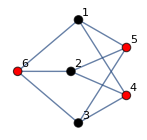

```mathematica
W={1,2,3,4,5,6};
F={1->4,1->5,1->6,2->4,2->5,2->6,3->4,3->5,3->6};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### e.

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Rojo

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Negro

Vértice 7, color Rojo

Vértice 8, color Rojo

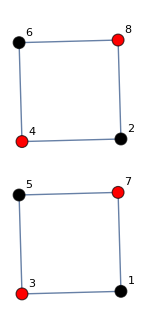

```mathematica
W={1,2,3,4,5,6,7,8};
F={1->3,1->7,2->4,2->8,3->5,4->6,5->7,6->8};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```